```mathematica
SetDirectory[NotebookDirectory[]];
```

## Orthoganal Matricies

```mathematica
ShearingMatrix[θ,{1,0},{0,1}]
```

{{1,Tan[θ]},{0,1}}

```mathematica
Transpose[{{1,Tan[θ]},{0,1}}]
```

{{1,0},{Tan[θ],1}}

```mathematica
Inverse[{{1,Tan[θ]},{0,1}}]
```

{{1,-Tan[θ]},{0,1}}

```mathematica
eqn=Inverse@({{a, b}, {c, d}})==({{a, c}, {b, d}})
```

{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}=={{a,c},{b,d}}

```mathematica
Reduce[eqn, a b+]
```

((c==-√(1-d^2)||c==√(1-d^2))&&(b==-√(1-d^2)||b==√(1-d^2))&&c≠0&&a==-(b d)/c)||((d==-1||d==1)&&c==0&&b==0&&(a==-1||a==1))

## Vectors and Matricies as Data

```mathematica
t = Import["data/1998DailyTempBos.csv"][[All,1]];
sound=Import["data/english_horn.wav"];
x=sound[[1,1,1]];
fs=sound[[1,2]];
```

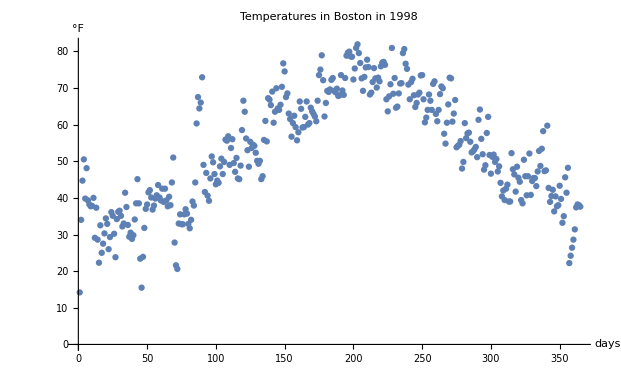

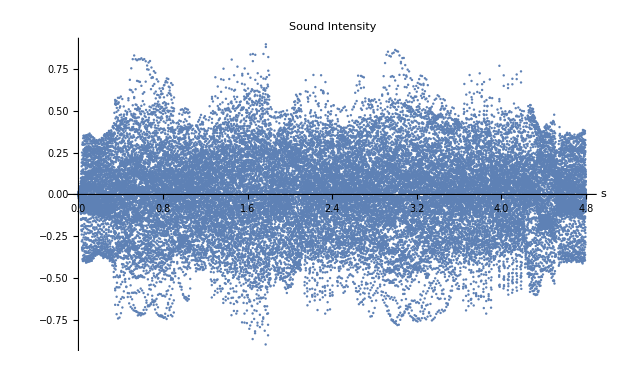

```mathematica
days=Range[Quantity[1, "Days"],Quantity[365, "Days"]];
ListPlot[Transpose[{days, t Quantity[, "DegreesFahrenheitDifference"]}],AxesLabel->Automatic,PlotLabel->"Temperatures in Boston in 1998"]
times =  1/fs*Range[Length[x]]Quantity[, "Seconds"];
ListPlot[Transpose[{times, x}], AxesLabel->Automatic, PlotLabel->"Sound Intensity"]
```

```mathematica
ListPlay[x]
```

-Graphics-

### 4

```mathematica
d=DiagonalMatrix[Join[{1},ConstantArray[1/3,363],{1}]]+DiagonalMatrix[Join[{0},ConstantArray[1/3,363]],1]+DiagonalMatrix[Join[ConstantArray[1/3,363],{0}],-1];
```

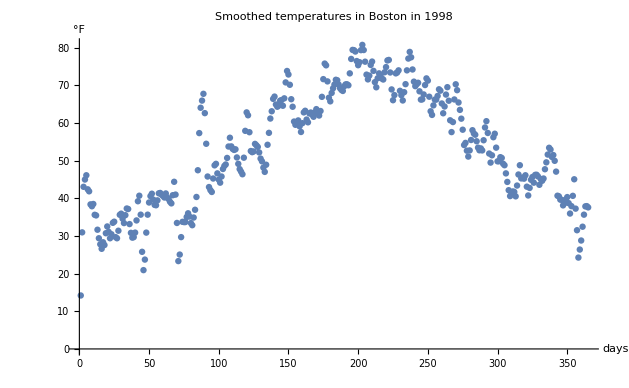

```mathematica
ListPlot[Transpose[{days, d.t Quantity[, "DegreesFahrenheitDifference"]}],AxesLabel->Automatic,PlotLabel->"Smoothed temperatures in Boston in 1998"]
```

### 8

```mathematica
ListPlay[x]
```

-Graphics-

```mathematica
applyKernel[k_,l_]:=Module[{circular, halfn},
halfn = Floor[Length@k/2];
circular=Sum[k[[kelem]]*RotateLeft[l,kelem-halfn-1],{kelem,Length@k}];
(* Fix the ends *)
circular[[1;;halfn]]=l[[1;;halfn]];
circular[[-halfn;;-1]]=l[[-halfn;;-halfn]];
Return@circular
]
```

```mathematica
ListPlay[applyKernel[ConstantArray[1/3,101], x]]
```

-Graphics-

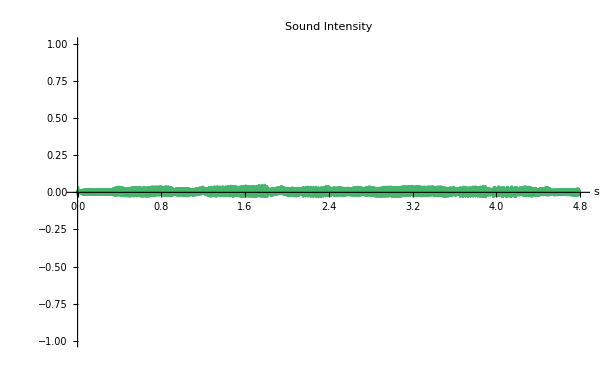

```mathematica
ListPlot[Transpose[{times, applyKernel[ConstantArray[1/101,101], x]}], AxesLabel->Automatic, PlotLabel->"Sound Intensity",PlotRange->{-1,1}]
```

```mathematica
applyKernel[{.01,.1,1},Range[10]]
```

{1,3.21,4.32,5.43,6.54,7.65,8.76,9.87,10.98,10}

### 9

```mathematica
ListConvolve[{-1,1,0},x]
```

{0.0050354,0.00268555,-0.00134277,0.00253296,0.00292969,0.00164795,0.000335693,0.00134277,38382,-0.0141296,-0.000823975,0.00466919,-0.00253296,-0.00427246,-0.00323486,-0.00112915,0.000274658}
 |  |  |  |

```mathematica
ListPlay[%]
```

-Graphics-

```mathematica
doOps[k_] := Module[{plotstuff},
plotstuff[x_]:=(
ListPlot[Transpose[{times, x}], AxesLabel->Automatic, PlotLabel->"Sound Intensity",PlotRange->{-1,1}]
)
Grid[
Transpose@{{
ListPlay[x],
plotstuff[x],
kernx=applyKernel[k,x];

}}
]
]
```

```mathematica
ListPlay[
```

Range::range: Range specification in Range[Thu 1 Jan 1998,Thu 31 Dec 1998] does not have appropriate bounds.

Range[Thu 1 Jan 1998,Thu 31 Dec 1998]

```mathematica
applyKernel[Range[3],Range[10]]
```

{1,14,20,26,32,38,44,50,56,10}

```mathematica
ListConvolve[Reverse@Range[3],Range[10],{1,-1},0]
```

{3,8,14,20,26,32,38,44,50,56,29,10}

```mathematica
ImageData[Image
```